# Late time approaches to the Hubble tension deforming H(z), worsen the growth tension - G. Alestas and L. Perivolaropoulos - Figure 3

## Section III - Growth of Perturbations and the Growth Tension in Hubble Deformation Models

### Setting the Directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Various Values

```mathematica
(* Planck values as given in 1502.01589 (Table 3, column 4) *)
ompl=0.315;
σ8pl=0.831;
h0pl=0.674; 
obh2=0.0224;
orh2=(1+3.046*7/8*(4/11)^(4/3))2.473*10^(-5);
omh2=ompl h0pl^2;
h0r=0.741;
zrec[om_,obh2_,h_]:=1048(1+0.00124(obh2)^-0.738)(1+((0.0783(obh2)^-0.238)/(1+39.5(obh2)^0.763))(omh2)^(0.560/(1+21.1(obh2)^1.81)));
```

### Import the Data

```mathematica
(* Import the Robust Growth Data from https://arxiv.org/pdf/1806.10822.pdf*)
datagrowth=Import[".\\data\\data_growth_2018_main.txt","Table"];
(* Import the chains for CMB obtained using the MGCosmoMC package *)

chain1=Import[".\\data\\lcdm\\2021-02-16_500000__1.txt","Table"];
chain2=Import[".\\data\\lcdm\\2021-02-16_500000__2.txt","Table"];
chain3=Import[".\\data\\lcdm\\2021-02-16_500000__3.txt","Table"];
chain4=Import[".\\data\\lcdm\\2021-02-16_500000__4.txt","Table"];
chain5=Import[".\\data\\lcdm\\2021-02-16_500000__5.txt","Table"];
chain6=Import[".\\data\\lcdm\\2021-02-16_500000__6.txt","Table"];

chain7=Import[".\\data\\cpl15\\2021-02-14_500000__1.txt","Table"];
chain8=Import[".\\data\\cpl15\\2021-02-14_500000__2.txt","Table"];
chain9=Import[".\\data\\cpl15\\2021-02-14_500000__3.txt","Table"];
chain10=Import[".\\data\\cpl15\\2021-02-14_500000__4.txt","Table"];
chain11=Import[".\\data\\cpl15\\2021-02-14_500000__5.txt","Table"];
chain12=Import[".\\data\\cpl15\\2021-02-14_500000__6.txt","Table"];

chain13=Import[".\\data\\cpl122\\2021-02-11_500000__1.txt","Table"];
chain14=Import[".\\data\\cpl122\\2021-02-11_500000__2.txt","Table"];
chain15=Import[".\\data\\cpl122\\2021-02-11_500000__3.txt","Table"];
chain16=Import[".\\data\\cpl122\\2021-02-11_500000__4.txt","Table"];
chain17=Import[".\\data\\cpl122\\2021-02-11_500000__5.txt","Table"];
chain18=Import[".\\data\\cpl122\\2021-02-11_500000__6.txt","Table"];
chain19=Import[".\\data\\cpl122\\2021-02-11_500000__7.txt","Table"];

chain20=Import[".\\data\\cpl173\\2021-02-14_500000__1.txt","Table"];
chain21=Import[".\\data\\cpl173\\2021-02-14_500000__2.txt","Table"];
chain22=Import[".\\data\\cpl173\\2021-02-14_500000__3.txt","Table"];
chain23=Import[".\\data\\cpl173\\2021-02-14_500000__4.txt","Table"];
chain24=Import[".\\data\\cpl173\\2021-02-14_500000__5.txt","Table"];
chain25=Import[".\\data\\cpl173\\2021-02-14_500000__6.txt","Table"];

chain26=Import[".\\data\\cpl11\\2021-02-27_500000__1.txt","Table"];
chain27=Import[".\\data\\cpl11\\2021-02-27_500000__2.txt","Table"];
chain28=Import[".\\data\\cpl11\\2021-02-27_500000__3.txt","Table"];
chain29=Import[".\\data\\cpl11\\2021-02-27_500000__4.txt","Table"];
chain30=Import[".\\data\\cpl11\\2021-02-27_500000__5.txt","Table"];
chain31=Import[".\\data\\cpl11\\2021-02-27_500000__6.txt","Table"];

chain32=Import[".\\data\\cpl1\\2021-02-28_500000__1.txt","Table"];
chain33=Import[".\\data\\cpl1\\2021-02-28_500000__2.txt","Table"];
chain34=Import[".\\data\\cpl1\\2021-02-28_500000__3.txt","Table"];
chain35=Import[".\\data\\cpl1\\2021-02-28_500000__4.txt","Table"];
chain36=Import[".\\data\\cpl1\\2021-02-28_500000__5.txt","Table"];
chain37=Import[".\\data\\cpl1\\2021-02-28_500000__6.txt","Table"];
```

```mathematica
dchi[nsig_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]/.M->2//N
nsig[dchi1_]:=FindRoot[dchi[nsig1]==dchi1,{nsig1,1}][[1,2]]
dchi2[nsig_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]/.M->2//N
nsig2[dchi1_]:=FindRoot[dchi2[nsig1]==dchi1,{nsig1,3}][[1,2]]
```

### Analysis of the Chains

```mathematica
(* Burn in Phase - 30% of the data should be excluded *)
MCMCchain1=chain1[[Round[0.3Length[chain1]];;-1]];
MCMCchain2=chain2[[Round[0.3Length[chain2]];;-1]];
MCMCchain3=chain3[[Round[0.3Length[chain3]];;-1]];
MCMCchain4=chain4[[Round[0.3Length[chain4]];;-1]];
MCMCchain5=chain5[[Round[0.3Length[chain5]];;-1]];
MCMCchain6=chain6[[Round[0.3Length[chain6]];;-1]];

MCMCchain7=chain7[[Round[0.3Length[chain7]];;-1]];
MCMCchain8=chain8[[Round[0.3Length[chain8]];;-1]];
MCMCchain9=chain9[[Round[0.3Length[chain9]];;-1]];
MCMCchain10=chain10[[Round[0.3Length[chain10]];;-1]];
MCMCchain11=chain11[[Round[0.3Length[chain11]];;-1]];
MCMCchain12=chain12[[Round[0.3Length[chain12]];;-1]];


MCMCchain13=chain13[[Round[0.3Length[chain13]];;-1]];
MCMCchain14=chain14[[Round[0.3Length[chain14]];;-1]];
MCMCchain15=chain15[[Round[0.3Length[chain15]];;-1]];
MCMCchain16=chain16[[Round[0.3Length[chain16]];;-1]];
MCMCchain17=chain17[[Round[0.3Length[chain17]];;-1]];
MCMCchain18=chain18[[Round[0.3Length[chain18]];;-1]];
MCMCchain19=chain19[[Round[0.3Length[chain19]];;-1]];

MCMCchain20=chain20[[Round[0.3Length[chain20]];;-1]];
MCMCchain21=chain21[[Round[0.3Length[chain21]];;-1]];
MCMCchain22=chain22[[Round[0.3Length[chain22]];;-1]];
MCMCchain23=chain23[[Round[0.3Length[chain23]];;-1]];
MCMCchain24=chain24[[Round[0.3Length[chain24]];;-1]];
MCMCchain25=chain25[[Round[0.3Length[chain25]];;-1]];

MCMCchain26=chain26[[Round[0.3Length[chain26]];;-1]];
MCMCchain27=chain27[[Round[0.3Length[chain27]];;-1]];
MCMCchain28=chain28[[Round[0.3Length[chain28]];;-1]];
MCMCchain29=chain29[[Round[0.3Length[chain29]];;-1]];
MCMCchain30=chain30[[Round[0.3Length[chain30]];;-1]];
MCMCchain31=chain31[[Round[0.3Length[chain31]];;-1]];

MCMCchain32=chain32[[Round[0.3Length[chain32]];;-1]];
MCMCchain33=chain33[[Round[0.3Length[chain33]];;-1]];
MCMCchain34=chain34[[Round[0.3Length[chain34]];;-1]];
MCMCchain35=chain35[[Round[0.3Length[chain35]];;-1]];
MCMCchain36=chain36[[Round[0.3Length[chain36]];;-1]];
MCMCchain37=chain37[[Round[0.3Length[chain37]];;-1]];
```

```mathematica
(* Join the two lists *) 
MCMClcdm=Join[MCMCchain1,MCMCchain2,MCMCchain3,MCMCchain4,MCMCchain5,MCMCchain6];

MCMCcpl15=Join[MCMCchain7,MCMCchain8,MCMCchain9,MCMCchain10,MCMCchain11,MCMCchain12];
MCMCcpl122=Join[MCMCchain13,MCMCchain14,MCMCchain15,MCMCchain16,MCMCchain17,MCMCchain18,MCMCchain19];
MCMCcpl173=Join[MCMCchain20,MCMCchain21,MCMCchain22,MCMCchain23,MCMCchain24,MCMCchain25];
MCMCcpl11=Join[MCMCchain26,MCMCchain27,MCMCchain28,MCMCchain29,MCMCchain30,MCMCchain31];
MCMCcpl1=Join[MCMCchain32,MCMCchain33,MCMCchain34,MCMCchain35,MCMCchain36,MCMCchain37];
```

```mathematica
(* Position of the minimum log(L)*)
bflcdm=MCMClcdm[[Position[MCMClcdm,Min[MCMClcdm[[All,2]]]][[1,1]]]];

bfcpl15=MCMCcpl15[[Position[MCMCcpl15,Min[MCMCcpl15[[All,2]]]][[1,1]]]];
bfcpl122=MCMCcpl122[[Position[MCMCcpl122,Min[MCMCcpl122[[All,2]]]][[1,1]]]];
bfcpl173=MCMCcpl173[[Position[MCMCcpl173,Min[MCMCcpl173[[All,2]]]][[1,1]]]];
bfcpl1=MCMCcpl1[[Position[MCMCcpl1,Min[MCMCcpl1[[All,2]]]][[1,1]]]];
bfcpl11=MCMCcpl11[[Position[MCMCcpl11,Min[MCMCcpl11[[All,2]]]][[1,1]]]];
```

```mathematica
(* Actual χ^2=2 log(L) *)
chi2lcdm=2*Min[MCMClcdm[[All,2]]]

chi2cpl15=2*Min[MCMCcpl15[[All,2]]]
chi2cpl122=2*Min[MCMCcpl122[[All,2]]]
chi2cpl173=2*Min[MCMCcpl173[[All,2]]]
chi2cpl11=2*Min[MCMCcpl11[[All,2]]]
chi2cpl1=2*Min[MCMCcpl1[[All,2]]]
```

2771.96

2772.72

2770.26

2787.12

2768.68

2768.1

```mathematica
(* Positions of the two variables you want to plot. In our case we choose Subscript[Ω, 0m] and Subscript[σ, 8] *)
pp={26,30};

ll={31,35};
(* Option to obtain smoother contours *)
smoothing=0.01;
(* Obtain all the values of the two parameters from the chains *)
dataomσ8lcdm=MCMClcdm[[All,ll]];

dataomσ8cpl15=MCMCcpl15[[All,ll]];
dataomσ8cpl122=MCMCcpl122[[All,ll]];
dataomσ8cpl173=MCMCcpl173[[All,ll]];

dataomσ8cpl11=MCMCcpl11[[All,ll]];
dataomσ8cpl1=MCMCcpl1[[All,ll]];
(* Calculate the smooth kernel distribution*)
skdlcdm=SmoothKernelDistribution[dataomσ8lcdm,smoothing];

skdcpl15=SmoothKernelDistribution[dataomσ8cpl15,smoothing];
skdcpl122=SmoothKernelDistribution[dataomσ8cpl122,smoothing];
skdcpl173=SmoothKernelDistribution[dataomσ8cpl173,smoothing];
skdcpl1=SmoothKernelDistribution[dataomσ8cpl1,smoothing];
skdcpl11=SmoothKernelDistribution[dataomσ8cpl11,smoothing];

(* Calculate the probability density function *)
pdflcdm=PDF[skdlcdm,dataomσ8lcdm];

pdfcpl15=PDF[skdcpl15,dataomσ8cpl15];
pdfcpl122=PDF[skdcpl122,dataomσ8cpl122];
pdfcpl173=PDF[skdcpl173,dataomσ8cpl173];

pdfcpl11=PDF[skdcpl11,dataomσ8cpl11];
pdfcpl1=PDF[skdcpl1,dataomσ8cpl1];
contourslcdm=Quantile[pdflcdm,1-Erf[nn/(√2)]/.nn->{1,2,3}//N];
contourscpl15=Quantile[pdfcpl15,1-Erf[nn/(√2)]/.nn->{1,2,3}//N];
contourscpl122=Quantile[pdfcpl122,1-Erf[nn/(√2)]/.nn->{1,2,3}//N];
contourscpl173=Quantile[pdfcpl173,1-Erf[nn/(√2)]/.nn->{1,2,3}//N];
contourscpl11=Quantile[pdfcpl11,1-Erf[nn/(√2)]/.nn->{1,2,3}//N];
contourscpl1=Quantile[pdfcpl1,1-Erf[nn/(√2)]/.nn->{1,2,3}//N];
```

```mathematica
(* Find the best fit values for the selected parameters for ΛCDM and wCDM with w=-1.2 *)
bflcdm=dataomσ8lcdm//Mean

bfcpl15=dataomσ8cpl15//Mean
bfcpl122=dataomσ8cpl122//Mean
bfcpl173=dataomσ8cpl173//Mean
bfcpl11=dataomσ8cpl11//Mean
bfcpl1=dataomσ8cpl1//Mean
```

{0.315984,0.811866}

{0.265544,0.860925}

{0.260206,0.872323}

{0.269211,0.842607}

{0.259885,0.873723}

{0.26,0.875335}

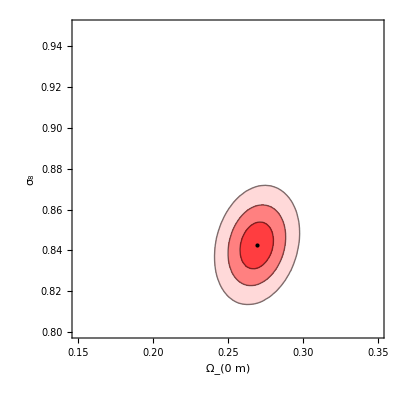

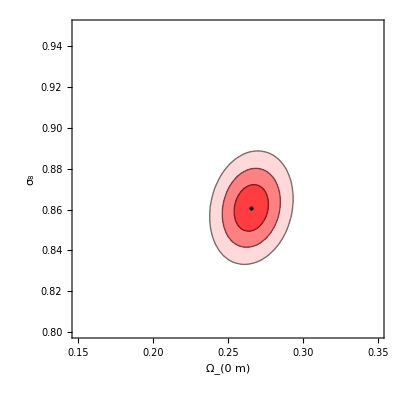

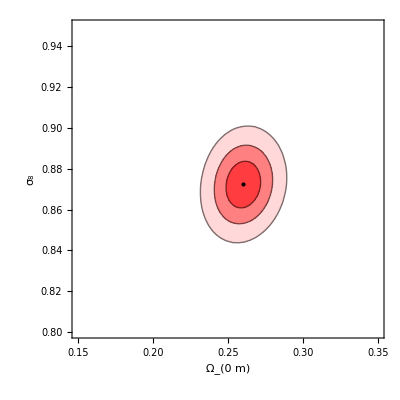

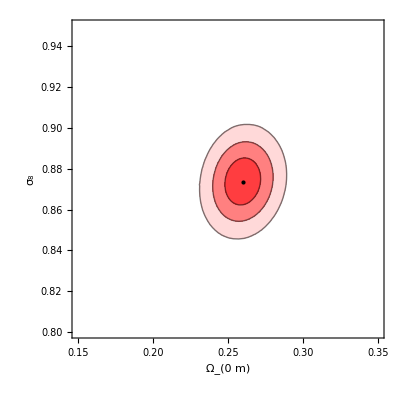

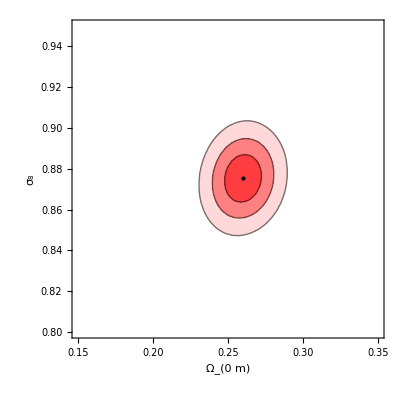

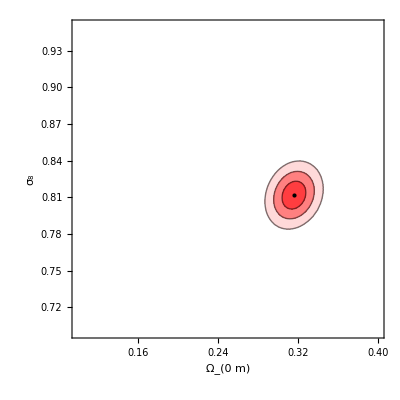

```mathematica
(* CMB contours *)
cpl173contour=ContourPlot[PDF[skdcpl173,{a,b}],{a, 0.15, 0.35},{b,.8,0.95},Contours->contourscpl173,ContourShading->{{White,Opacity[0]},LightRed,RGBColor[1,0.5,0.5],RGBColor[1,0.24,0.25]},FrameLabel->{"Ω_(0  m)","σ_8"},BaseStyle->FontSize->18,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{PointSize[Medium],Black,Point[{bfcpl173[[1]],bfcpl173[[2]]}]}}]
cpl15contour=ContourPlot[PDF[skdcpl15,{a,b}],{a, 0.15, 0.35},{b,.8,0.95},Contours->contourscpl15,ContourShading->{{White,Opacity[0]},LightRed,RGBColor[1,0.5,0.5],RGBColor[1,0.24,0.25]},FrameLabel->{"Ω_(0  m)","σ_8"},BaseStyle->FontSize->18,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{PointSize[Medium],Black,Point[{bfcpl15[[1]],bfcpl15[[2]]}]}}]
cpl122contour=ContourPlot[PDF[skdcpl122,{a,b}],{a, 0.15, 0.35},{b,.8,0.95},Contours->contourscpl122,ContourShading->{{White,Opacity[0]},LightRed,RGBColor[1,0.5,0.5],RGBColor[1,0.24,0.25]},FrameLabel->{"Ω_(0  m)","σ_8"},BaseStyle->FontSize->18,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{PointSize[Medium],Black,Point[{bfcpl122[[1]],bfcpl122[[2]]}]}}]
cpl11contour=ContourPlot[PDF[skdcpl11,{a,b}],{a, 0.15, 0.35},{b,.8,0.95},Contours->contourscpl11,ContourShading->{{White,Opacity[0]},LightRed,RGBColor[1,0.5,0.5],RGBColor[1,0.24,0.25]},FrameLabel->{"Ω_(0  m)","σ_8"},BaseStyle->FontSize->18,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{PointSize[Medium],Black,Point[{bfcpl11[[1]],bfcpl11[[2]]}]}}]
cpl1contour=ContourPlot[PDF[skdcpl1,{a,b}],{a, 0.15, 0.35},{b,.8,0.95},Contours->contourscpl1,ContourShading->{{White,Opacity[0]},LightRed,RGBColor[1,0.5,0.5],RGBColor[1,0.24,0.25]},FrameLabel->{"Ω_(0  m)","σ_8"},BaseStyle->FontSize->18,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{PointSize[Medium],Black,Point[{bfcpl1[[1]],bfcpl1[[2]]}]}}]
lcdmcontour=ContourPlot[PDF[skdlcdm,{a,b}],{a, 0.1, 0.4},{b,.7,0.95},Contours->contourslcdm,ContourShading->{{White,Opacity[0]},LightRed,RGBColor[1,0.5,0.5],RGBColor[1,0.24,0.25]},FrameLabel->{"Ω_(0  m)","σ_8"},BaseStyle->FontSize->18,PlotRange->All,FrameStyle->Black,ClippingStyle->None,Epilog->{{PointSize[Medium],Black,Point[{bflcdm[[1]],bflcdm[[2]]}]}}]
```

### Growth Data Analysis - CPL

```mathematica
(* Add support for WiggleZ and SDSS data Cij *)
Cijwigglez=Import[".\\data\\Cij_WiggleZ.txt","Table"];
Cijsdss=Import[".\\data\\Cij_SDSS.txt","Table"];
```

```mathematica
(* Theoretical expressions *)
wcpl[z_,w0_,wa_]:=w0+wa z/(z+1)
decpl=Exp[3 Integrate[(1+wcpl[zp,w0,wa])/(1+zp),{zp,0,z},Assumptions->z>0]];

Hcpl[z_,om_,w0_,wa_]:=√(om (1+z)^3+orh2  (1+z)^4+(1 -om-orh2 )ⅇ^(3 (-(wa z)/(1+z)+(1+w0+wa) Log[1+z])))
amin=0.001;
dsol[om_?NumberQ,w0_?NumberQ,wa_?NumberQ]:=(dsol[om,w0,wa]=Module[{a},NDSolve[{-((3 om d[a] Hcpl[0,om,w0,wa]^2)/(2 a^5  Hcpl[1/a-1,om,w0,wa]^2))+d'[a] (3/a+D[Hcpl[1/a-1,om,w0,wa],a]/Hcpl[1/a-1,om,w0,wa])+d''[a]==0,d[amin]==amin,d'[amin]==1},d,{a,amin,1}][[1]]])
(* The growth rate and fσ8 *)
Da[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ]:=d[a]/.dsol[om,w0,wa]
fa[aa_,om_,w0_,wa_]:=a d'[a]/d[a]/.a->aa/.dsol[om,w0,wa]
fσ8[a_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,w0,wa])/Da[1,om,w0,wa] fa[aa,om,w0,wa]/.aa->a
fσ8z[z_?NumberQ,om_?NumberQ,w0_?NumberQ,wa_?NumberQ,σ8_?NumberQ]:=(σ8 Da[aa,om,w0,wa])/Da[1,om,w0,wa] fa[aa,om,w0,wa]/.aa->1/(1+z)
Da[1,ompl,-1,0]
```

0.749006

```mathematica
Wigglez={13,14,15};
SDSS={19,20,21,22};
Cijfs81=DiagonalMatrix[datagrowth[[All,3]]^2];
Cijfs81[[Wigglez,Wigglez]]=Cijwigglez;
Cijfs81[[SDSS,SDSS]]=Cijsdss;
InvCijfs81=Inverse[Cijfs81];
(*Fiducial correction from robust paper*)
omf={0.3,0.3,0.266,0.3,0.31,0.3,0.27,0.27,0.25,0.25,0.274,0.307115,0.27,0.27,0.27,0.3,0.3,0.27,0.31,0.31,0.31,0.31};
```

```mathematica
(* χ^2 correlated term *)
vecgr[data_,w0_,wa_,om_,σ8_]:=Table[data[[i,2]]-fσ8[1/(1+data[[i,1]]),om,w0,wa,σ8],{i,1,Length[data]}]
chi2corr[data_,w0_,wa_,om_,σ8_]:=vecgr[data,w0,wa,om,σ8].InvCijfs81.vecgr[data,w0,wa,om,σ8]
```

```mathematica
(* Planck Value for Subscript[σ, 8] *)
fmins8pl=FindMinimum[chi2corr[datagrowth,-1,0,om,σ8pl],{om,.3,.31}]
```

{12.4134,{om→0.23569}}

```mathematica
(* Minimize χ^2 over different parameters *)
fmwc=FindMinimum[chi2corr[datagrowth,-1,0,om,σ8],{om,.3,.31},{σ8,.8,.81}]
fmwc3=FindMinimum[chi2corr[datagrowth,-1.5,1.05,om,σ8],{om,.3,.31},{σ8,.8,.81}]
fmwc4=FindMinimum[chi2corr[datagrowth,-1.73,1.72,om,σ8],{om,.3,.31},{σ8,.8,.81}]
fmwc5=FindMinimum[chi2corr[datagrowth,-1.22,0,om,σ8],{om,.3,.31},{σ8,.8,.81}]
fmwc6=FindMinimum[chi2corr[datagrowth,-1.1,-0.497,om,σ8],{om,.3,.31},{σ8,.8,.81}]
fmwc7=FindMinimum[chi2corr[datagrowth,-1,-0.93,om,σ8],{om,.3,.31},{σ8,.8,.81}]
ombfwc=fmwc[[2,1,2]];
σ8bfwc=fmwc[[2,2,2]];
ombfwc3=fmwc3[[2,1,2]];
σ8bfwc3=fmwc3[[2,2,2]];
ombfwc4=fmwc4[[2,1,2]];
σ8bfwc4=fmwc4[[2,2,2]];
ombfwc5=fmwc5[[2,1,2]];
σ8bfwc5=fmwc5[[2,2,2]];
ombfwc6=fmwc6[[2,1,2]];
σ8bfwc6=fmwc6[[2,2,2]];
ombfwc7=fmwc7[[2,1,2]];
σ8bfwc7=fmwc7[[2,2,2]];
```

{12.3644,{om→0.246222,σ8→0.815744}}

{13.0403,{om→0.249358,σ8→0.767524}}

{13.5774,{om→0.249219,σ8→0.753968}}

{12.6418,{om→0.255501,σ8→0.774357}}

{12.549,{om→0.25926,σ8→0.775388}}

{12.504,{om→0.262808,σ8→0.775595}}

```mathematica
deltachilcdm= chi2corr[datagrowth,-1,0,bflcdm[[1]],bflcdm[[2]]]-chi2corr[datagrowth,-1,0,ombfwc,σ8bfwc]
deltachi1=chi2corr[datagrowth,-1,-0.93,bfcpl1[[1]],bfcpl1[[2]]]-chi2corr[datagrowth,-1,-0.93,ombfwc7,σ8bfwc7]
deltachi11= chi2corr[datagrowth,-1.1,-0.497,bfcpl11[[1]],bfcpl11[[2]]]-chi2corr[datagrowth,-1.1,-0.497,ombfwc6,σ8bfwc6]
deltachi15= chi2corr[datagrowth,-1.5,1.05,bfcpl15[[1]],bfcpl15[[2]]]-chi2corr[datagrowth,-1.5,1.05,ombfwc3,σ8bfwc3]
deltachi122= chi2corr[datagrowth,-1.22,0,bfcpl122[[1]],bfcpl122[[2]]]-chi2corr[datagrowth,-1.22,0,ombfwc5,σ8bfwc5]
deltachi173= chi2corr[datagrowth,-1.73,1.72,bfcpl173[[1]],bfcpl173[[2]]]-chi2corr[datagrowth,-1.73,1.72,ombfwc4,σ8bfwc4]
```

6.26049

11.2978

11.7942

14.8008

12.7698

14.6931

```mathematica
dchitab[nsig_]:=2 InverseGammaRegularized[M/2,1-Erf[nsig/(√2)]]/.M->2//N
nsigtab[dchi1_]:=FindRoot[dchitab[nsig1]==dchi1,{nsig1,3}][[1,2]]
```

```mathematica
nsigtab[deltachi1]
```

2.91813

```mathematica
bflcdm[[1]]
```

0.315984

```mathematica
bflcdm[[2]]
```

0.811866

```mathematica
(* Growth contours for ΛCDM *)
contlcdm=ContourPlot[chi2corr[datagrowth,-1,0,om,σ8],{om,0.1,0.6},{σ8,0.6,0.95},Contours->{fmwc[[1]]+dchi[1],fmwc[[1]]+dchi[2],fmwc[[1]]+dchi[3]},ContourShading->{Cyan,RGBColor[0.78,1,0.96],LightCyan, White}];
(* Growth contours for wCDM with w=-1.22 *)
contcpl122=ContourPlot[chi2corr[datagrowth,-1.22,0,om,σ8],{om,0.1,0.6},{σ8,0.6,0.95},Contours->{fmwc5[[1]]+dchi[1],fmwc5[[1]]+dchi[2],fmwc5[[1]]+dchi[3]},ContourShading->{Cyan,RGBColor[0.78,1,0.96],LightCyan, White}];
(* Growth contours for CPL with w=-1.5 *)
contcpl15=ContourPlot[chi2corr[datagrowth,-1.5,1.05,om,σ8],{om,0.1,0.6},{σ8,0.6,0.95},Contours->{fmwc3[[1]]+dchi[1],fmwc3[[1]]+dchi[2],fmwc3[[1]]+dchi[3]},ContourShading->{Cyan,RGBColor[0.78,1,0.96],LightCyan, White}];
(* Growth contours for CPL with w=-1.73 *)
contcpl173=ContourPlot[chi2corr[datagrowth,-1.73,1.72,om,σ8],{om,0.1,0.6},{σ8,0.6,0.95},Contours->{fmwc4[[1]]+dchi[1],fmwc4[[1]]+dchi[2],fmwc4[[1]]+dchi[3]},ContourShading->{Cyan,RGBColor[0.78,1,0.96],LightCyan, White}];
(* Growth contours for CPL with w=-1.1 *)
contcpl11=ContourPlot[chi2corr[datagrowth,-1.1,-0.497,om,σ8],{om,0.1,0.6},{σ8,0.6,0.95},Contours->{fmwc6[[1]]+dchi[1],fmwc6[[1]]+dchi[2],fmwc6[[1]]+dchi[3]},ContourShading->{Cyan,RGBColor[0.78,1,0.96],LightCyan, White}];
(* Growth contours for CPL with w=-1 *)
contcpl1=ContourPlot[chi2corr[datagrowth,-1,-0.93,om,σ8],{om,0.1,0.6},{σ8,0.6,0.95},Contours->{fmwc7[[1]]+dchi[1],fmwc7[[1]]+dchi[2],fmwc7[[1]]+dchi[3]},ContourShading->{Cyan,RGBColor[0.78,1,0.96],LightCyan, White}];
```

```mathematica
(* Overlap the CMB and growth contours for CPL*)
cont0=Show[{contlcdm,lcdmcontour},Epilog->{{PointSize[Medium],Black,Point[{ombfwc,σ8bfwc}]},
{PointSize[Medium],Black,Point[{bflcdm[[1]],bflcdm[[2]]}]},Text["fσ_8 Likelihood Contours for ΛCDM",{0.42,0.6}],Text["CMB Best-fit for ΛCDM",{0.52,0.85}]},Frame->{{True,True},{False,True}},FrameLabel->{None,"σ_8"},PlotRange->{{0.1,0.7},{0.59,0.95}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},FrameStyle->Directive[Black],ImageSize->Medium];
cont1=Show[{contcpl122,cpl122contour},Epilog->{{PointSize[Medium],Black,Point[{ombfwc5,σ8bfwc5}]},
{PointSize[Medium],Black,Point[{bfcpl122[[1]],bfcpl122[[2]]}]},Text["fσ_8 Likelihood Contours for w_0=-1.22, w_1=0",{0.42,0.6}],Text["CMB Best-fit for w_0=-1.22, w_1=0",{0.49,0.91}]},FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.1,0.7},{0.59,0.95}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},FrameStyle->Directive[Black],ImageSize->Medium];
cont2=Show[{contcpl15,cpl15contour},Epilog->{{PointSize[Medium],Black,Point[{ombfwc3,σ8bfwc3}]},
{PointSize[Medium],Black,Point[{bfcpl15[[1]],bfcpl15[[2]]}]},Text["fσ_8 Likelihood Contours for w_0=-1.5, w_1=1.05",{0.42,0.6}],Text["CMB Best-fit for w_0=-1.5, w_1=1.05",{0.48,0.9}]},Frame->{{False,True},{True,True}},FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.1,0.7},{0.59,0.95}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},FrameStyle->Directive[Black],ImageSize->Medium];
cont3=Show[{contcpl173,cpl173contour},Epilog->{{PointSize[Medium],Black,Point[{ombfwc4,σ8bfwc4}]},
{PointSize[Medium],Black,Point[{bfcpl173[[1]],bfcpl173[[2]]}]},Text["fσ_8 Likelihood Contours for w_0=-1.73, w_1=1.72",{0.42,0.6}],Text["CMB Best-fit for w_0=-1.73, w_1=1.72",{0.47,0.89}]},Frame->{{False,True},{True,True}},FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.1,0.7},{0.59,0.95}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},FrameStyle->Directive[Black],ImageSize->Medium];
cont4=Show[{contcpl11,cpl11contour},Epilog->{{PointSize[Medium],Black,Point[{ombfwc6,σ8bfwc6}]},
{PointSize[Medium],Black,Point[{bfcpl11[[1]],bfcpl11[[2]]}]},Text["fσ_8 Likelihood Contours for w_0=-1.1, w_1=-0.497",{0.4,0.6}],Text["CMB Best-fit for w_0=-1.1, w_1=-0.497",{0.47,0.92}]},Frame->{{False,True},{False,True}},FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.1,0.7},{0.59,0.95}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},FrameStyle->Directive[Black],ImageSize->Medium];
cont5=Show[{contcpl1,cpl1contour},Epilog->{{PointSize[Medium],Black,Point[{ombfwc7,σ8bfwc7}]},
{PointSize[Medium],Black,Point[{bfcpl1[[1]],bfcpl1[[2]]}]},Text["fσ_8 Likelihood Contours for w_0=-1, w_1=-0.93",{0.42,0.6}],Text["CMB Best-fit for w_0=-1, w_1=-0.93",{0.47,0.92}]},Frame->{{False,True},{False,True}},FrameLabel->{"Ω_(0  m)","σ_8"},PlotRange->{{0.1,0.7},{0.59,0.95}},PlotRangeClipping->True,BaseStyle->{FontFamily->"Times",16},FrameStyle->Directive[Black],ImageSize->Medium];
```

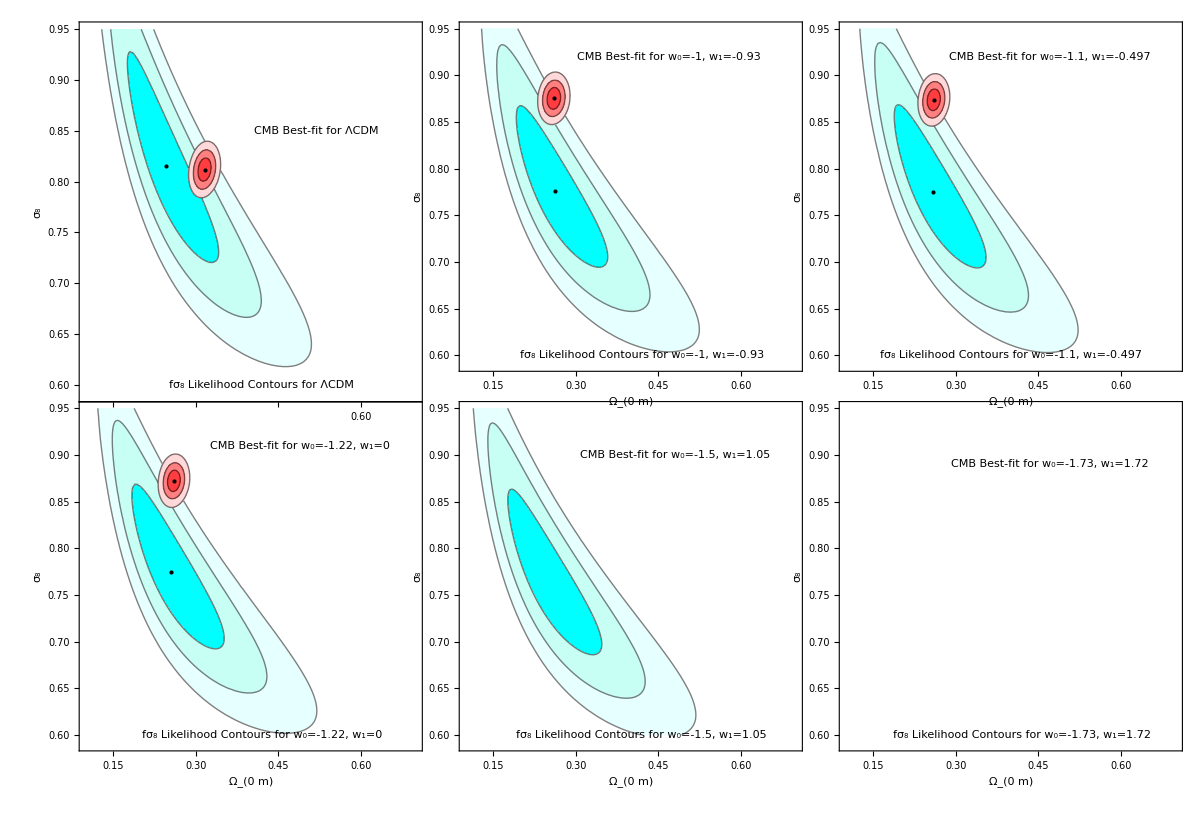

```mathematica
fig5=GraphicsGrid[{{cont0,cont5,cont4},{cont1,cont2,cont3}},Spacings->-49,ImageSize->1200]
```

```mathematica
Export[NotebookDirectory[]<>"fig3.pdf",fig5,ImageResolution->1000];
```